```mathematica
M=4866;m=2433;k2=80000;c2=10000;omega=2.2143;k1=1025*9.8*Pi;
f=4890;c1=167.8395;m0=1165.992;
start=510;stop=520;dim=1;
P2[cm2_]:=Sum[cm2*((x1'[i]-x2'[i])^2)*dim,{i,start,stop,dim}]/. NDSolve[{m*x2''[t]==k2*(x1[t]-x2[t])+cm2*(x1'[t]-x2'[t]),f*Cos[omega*t]==k2*(x1[t]-x2[t])+cm2*(x1'[t]-x2'[t])+k1*x1[t]+c1*x1'[t]+m0*x1''[t]+M*x1''[t],x1[0]==x2[0]==x1'[0]==x2'[0]==0},{x1,x2},{t,start,stop}]
(*FindMaximum[{First[P2[x]],0<=x<=10000},{x,5000}]*)
DrawP2[pStart_,pStop_,pStepNum_]:=ListLinePlot[Table[{i*(pStop-pStart)/pStepNum,First[P2[i]]},{i,Range[pStart,pStop,(pStop-pStart)/pStepNum]}]]
(*DrawP2Diff[start_,stop_,stepNum_]:=ListLinePlot[Table[{i*1000,First[P2'[i]]},{i,Range[start,stop,(stop-start)/stepNum]}]]*)
(*DrawP2[0,100000,100]*)
(*DrawP2[30000,40000,100]*)
(*DrawP2[34000,36000,100]*)
(*DrawP2Diff[34000,36000,100]*)
(*ListLinePlot[Table[First[P2[i]],{i,Range[0,100000,1000]}]]*)
First[P2[100]]
```

14.6552

from wolframclient.evaluation import WolframLanguageSession
from wolframclient.language import wl, wlexpr
session = WolframLanguageSession()

def PP2(x, d): return session.evaluate(wl.Evaluate(wlexpr(f'First[PPP2[{x}]-PPP2[{x-d}]]')))
print(PP2(100, 1))
print(type(PP2(100, 1)))

Times[-1, Global`PPP2[99]]

<class 'wolframclient.language.expression.WLFunction'>

def find(start, stop, d, f, esp=1):
	m = (start + stop) / 2
	v = f(m, d)
	print(v)
	if abs(v) < esp:
		return [m, v]
	if v < 0:
		return find(start, m, d, f)
	return find(m, stop, d, f)

ExternalFunction[…]

find(0, 100000, 1, PP2)

P2[50000.0]-P2[49999.0]

Plus[Times[-1, Global`P2[49999.0]], Global`P2[50000.0]]

Failure[…]

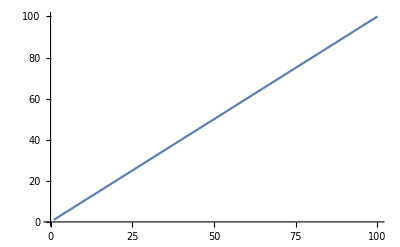

```mathematica
ListLinePlot[Range[100]]
```

```mathematica
Clear["Global`*"];
d = 1;
l0 = 1; 
m = 1; 
k = 1;
c = 1;
g = 9.8;
kr = 1;
cr = 1;
Ib = 1;
Ia = 1;
Fw = 1;
M = 1;
Fx = 1;
xg = 0;
Mf = 1;
L = 1;
w = 1;
f = 1;

Fw := f * Cos[w*t];
Fx := 1 * Abs[zg'[t]];
Mx[t_] := 1 * Abs[th'[t]];
Mj[t_] := 1 * Abs[th[t]];
Mw[t_] := L * Cos[o*t];
za[t_] := zg[t] - d*Cos[th[t]];
th2[t_] := th[t] + ga[t]; 
xp[t_] := xg - d*Sin[th[t]] + l[t]*Sin[th2[t]]; 
zp[t_] := (-d)*Cos[th[t]] + l[t]*Cos[th2[t]]; 
F[t_] := k*(l[t] - l0) + c*l'[t];
Mab[t_] := kr*ga[t] + cr*ga'[t];
NDSolve[{
  m*xp''[t] == F[t]*Sin[th2[t]], 
  m*zp''[t] == F[t]*Cos[th2[t]] - m*g,
  Ib*th2''[t] == Mab[t] + F[t] * l[t],
  Fw[t] - M*g - F[t]*Cos[th2[t]] - Fx - Ff == M*zg''[t],
  Ia*th''[t] == -Mab[t] + F[t]*d + Mw[t] - Mx[t] - Mf - Mj[t],
l[t] == l0 - 1/k*(m*g + c/Cos[th2[t]]*(zp[t]-za[t])),
  th[0] == th'[0] == ga[0] == ga'[0] == l[0] == l'[0] == zg[0] == zg'[0] == 0}, {th, ga, zg, l}, {t, 0, 100}]
```

NDSolve::overdet: 因变量 {ga[t],l[t],th[t],zg[t]} 的个数少于方程个数，因此方程组是超定的.

NDSolve[{Sin[th[t]] th'[t]^2+2 Cos[ga[t]+th[t]] l'[t] (ga'[t]+th'[t])-l[t] Sin[ga[t]+th[t]] (ga'[t]+th'[t])^2+Sin[ga[t]+th[t]] l''[t]-Cos[th[t]] th''[t]+Cos[ga[t]+th[t]] l[t] (ga''[t]+th''[t])==Sin[ga[t]+th[t]] (-1+l[t]+l'[t]),Cos[th[t]] th'[t]^2-2 Sin[ga[t]+th[t]] l'[t] (ga'[t]+th'[t])-Cos[ga[t]+th[t]] l[t] (ga'[t]+th'[t])^2+Cos[ga[t]+th[t]] l''[t]+Sin[th[t]] th''[t]-l[t] Sin[ga[t]+th[t]] (ga''[t]+th''[t])==-9.8+Cos[ga[t]+th[t]] (-1+l[t]+l'[t]),ga''[t]+th''[t]==ga[t]+ga'[t]+l[t] (-1+l[t]+l'[t]),-9.8-Ff-Abs[zg'[t]]+Cos[t][t]-Cos[ga[t]+th[t]] (-1+l[t]+l'[t])==zg''[t],th''[t]==-2-Abs[th[t]]-Abs[th'[t]]+Cos[o t]-ga[t]+l[t]-ga'[t]+l'[t],l[t]==-8.8-Sec[ga[t]+th[t]] (Cos[ga[t]+th[t]] l[t]-zg[t]),th[0]==th'[0]==ga[0]==ga'[0]==l[0]==l'[0]==zg[0]==zg'[0]==0},{th,ga,zg,l},{t,0,100}]

```mathematica
aaa[t_] := t^2;
First[ggg]/.NDSolve[{aaa'[ggg'[t]] == 3, ggg[0]==0}, {ggg}, {t, 0, 100}]
```

First::normal: First[ggg] 中的位置 1 处应该是非原子表达式.

{{{0.,100.}}}

```mathematica
First[%1185]
```

InterpolatingFunction[…]

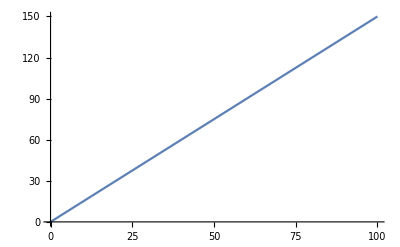

```mathematica
Plot[%1186[x],{x,0.,100.}]
```